```mathematica
Clear[R,ϵ];
```

```mathematica
S=(1/R)-(2p/((R-1)+√((R-1)^2+4*R*p)))
```

1/R-1.6/(-1+R+√((-1+R)^2+3.2 R))

```mathematica
V=(ϵ*(R-1)+ϵ*√((R-1)^2+4*R*p))/(2*R)
```

((-1+R) ϵ+√((-1+R)^2+3.2 R) ϵ)/(2 R)

```mathematica
p=0.8
```

0.8

```mathematica
Solve[(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)==0,ϵ]
```

{{ϵ→(0.5 (-2.+2. R+2. √(1.+1.2 R+R^2)-(4.8 R)/(1.-1. R-1. √(1.+1.2 R+R^2))+(1.6 R^2)/(1.-1. R-1. √(1.+1.2 R+R^2))+(1.6 R √(1.+1.2 R+R^2))/(1.-1. R-1. √(1.+1.2 R+R^2))-1. √(-(10.24 R^2 (0.5+0.8 R+0.5 R^2+0.5 √(1.+1.2 R+R^2)+0.5 R √(1.+1.2 R+R^2)))/((1.-1. R-1. √(1.+1.2 R+R^2))^2)+(2.-2. R-2. √(1.+1.2 R+R^2)+(4.8 R)/(1.-1. R-1. √(1.+1.2 R+R^2))-(1.6 R^2)/(1.-1. R-1. √(1.+1.2 R+R^2))-(1.6 R √(1.+1.2 R+R^2))/(1.-1. R-1. √(1.+1.2 R+R^2)))^2)))/(0.5+0.8 R+0.5 R^2+0.5 √(1.+1.2 R+R^2)+0.5 R √(1.+1.2 R+R^2))},{ϵ→(0.5 (-2.+2. R+2. √(1.+1.2 R+R^2)-(4.8 R)/(1.-1. R-1. √(1.+1.2 R+R^2))+(1.6 R^2)/(1.-1. R-1. √(1.+1.2 R+R^2))+(1.6 R √(1.+1.2 R+R^2))/(1.-1. R-1. √(1.+1.2 R+R^2))+√(-(10.24 R^2 (0.5+0.8 R+0.5 R^2+0.5 √(1.+1.2 R+R^2)+0.5 R √(1.+1.2 R+R^2)))/((1.-1. R-1. √(1.+1.2 R+R^2))^2)+(2.-2. R-2. √(1.+1.2 R+R^2)+(4.8 R)/(1.-1. R-1. √(1.+1.2 R+R^2))-(1.6 R^2)/(1.-1. R-1. √(1.+1.2 R+R^2))-(1.6 R √(1.+1.2 R+R^2))/(1.-1. R-1. √(1.+1.2 R+R^2)))^2)))/(0.5+0.8 R+0.5 R^2+0.5 √(1.+1.2 R+R^2)+0.5 R √(1.+1.2 R+R^2))}}

```mathematica
g[R_]:=(0.5 (-2.+2. R+2. √(1.+1.2000000000000002 R+R^2)-(4.800000000000001 R)/(1.-1. R-1. √(1.+1.2000000000000002 R+R^2))+(1.6 R^2)/(1.-1. R-1. √(1.+1.2000000000000002 R+R^2))+(1.6 R √(1.+1.2000000000000002 R+R^2))/(1.-1. R-1. √(1.+1.2000000000000002 R+R^2))-1. √(-((10.240000000000002 R^2 (0.5+0.8 R+0.5 R^2+0.5 √(1.+1.2000000000000002 R+R^2)+0.5 R √(1.+1.2000000000000002 R+R^2)))/(1.-1. R-1. √(1.+1.2000000000000002 R+R^2))^2)+(2.-2. R-2. √(1.+1.2000000000000002 R+R^2)+(4.800000000000001 R)/(1.-1. R-1. √(1.+1.2000000000000002 R+R^2))-(1.6 R^2)/(1.-1. R-1. √(1.+1.2000000000000002 R+R^2))-(1.6 R √(1.+1.2000000000000002 R+R^2))/(1.-1. R-1. √(1.+1.2000000000000002 R+R^2)))^2)))/(0.5+0.8 R+0.5 R^2+0.5 √(1.+1.2000000000000002 R+R^2)+0.5 R √(1.+1.2000000000000002 R+R^2))
```

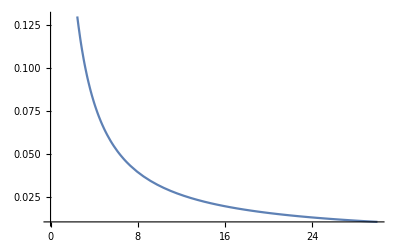

```mathematica
Plot[g[R],{R,0,30}]
```

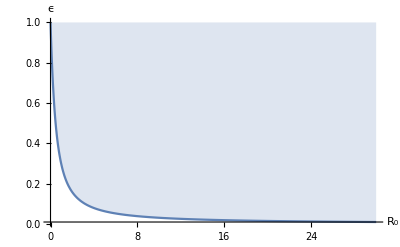

```mathematica
Plot[g[R],{R,0,30},Filling->Top,AxesLabel->{Subscript[R, 0],ϵ},PlotRange->Full]
```

```mathematica
m[R_]:=g[R-1]
```

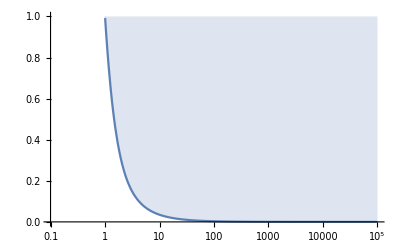

```mathematica
LogLinearPlot[m[R],{R,0.1,100000},Filling->Top,PlotRange->{{0,100000},{0,1}}]
```

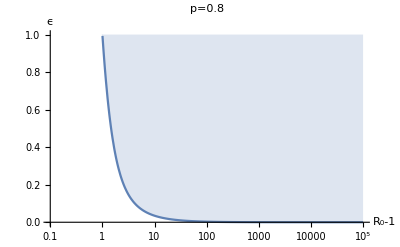

```mathematica
Show[%158,AxesLabel->{HoldForm[Subscript[R, 0]-1],HoldForm[ϵ]},PlotLabel->HoldForm[p=0.8],LabelStyle->{GrayLevel[0]}]
```